```mathematica
In this test we recurse over the children of K5 and note all Complete graphs
```

```mathematica
FindCompleteElementsOfK5[current_]:=Block[{result={}, children = DeleteDuplicates[Flatten [allGraphs[current,"children"]]]},
Table[ 
If [CompleteGraphQ[allGraphs[child,"graph"]],result=Append[result, child]];
result = Join[result,FindCompleteElementsOfK5[child]];
,  {child,  children}
];
result
]
```

```mathematica
Table[allGraphs[k,"colofourrealnull"],{k,FindCompleteElementsOfK5[lambdaKey]//DeleteDuplicates}]//Total
```

4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

```mathematica
Table[Labeled[allGraphs[k,"colofour"],allGraphs[k,"graph"]],{k,FindCompleteElementsOfK5[lambdaKey]//DeleteDuplicates}]
```

{v1x2x3x4x5-Graphics-,v1x2x35x4-Graphics-,v1x25x3x4-Graphics-,v1x24x3x5-Graphics-,v1x24x35-Graphics-,v14x2x3x5-Graphics-,v14x2x35-Graphics-,v14x25x3-Graphics-,v13x2x4x5-Graphics-,v13x25x4-Graphics-,v13x24x5-Graphics-}

```mathematica
Reduce[allGraphs[lambdaKey,"colofourrealnull"]==(Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]+allGraphs[k5Key,"colofourrealnull"])]
```

n12345==n1234x5/10+n1235x4/10+n1245x3/10+n124x35/5+n1345x2/10+n134x25/5+n135x24/5+n13x245/5-n13x24x5/10-n13x25x4/10+n14x235/5-n14x25x3/10-n14x2x35/10+n1x2345/10-n1x24x35/10

```mathematica
Reduce[allGraphs[lambdaKey,"colofourrealnull"]==(Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]])]
```

n12345==(7 n1234x5)/34+(7 n1235x4)/34+n123x45/17-n123x4x5/17+(7 n1245x3)/34+(2 n124x35)/17-n124x3x5/17+n125x34/17-n125x3x4/17+n12x345/17-n12x34x5/34-n12x35x4/34-n12x3x45/34+n12x3x4x5/34+(7 n1345x2)/34+(2 n134x25)/17-n134x2x5/17+(2 n135x24)/17-n135x2x4/17+(2 n13x245)/17-n13x24x5/17-n13x25x4/17-n13x2x45/34+n13x2x4x5/34+n145x23/17-n145x2x3/17+(2 n14x235)/17-n14x23x5/34-n14x25x3/17-n14x2x35/17+n14x2x3x5/34+n15x234/17-n15x23x4/34-n15x24x3/34-n15x2x34/34+n15x2x3x4/34+(7 n1x2345)/34-n1x234x5/17-n1x235x4/17-n1x23x45/34+n1x23x4x5/34-n1x245x3/17-n1x24x35/17+n1x24x3x5/34-n1x25x34/34+n1x25x3x4/34-n1x2x345/17+n1x2x34x5/34+n1x2x35x4/34+n1x2x3x45/34-n1x2x3x4x5/34

```mathematica
Reduce[0==Total[Table[allGraphs[k,"colofourrealnull"]/.n1x2x3x4x5->(18 n1234x5)/5+(18 n1235x4)/5+2 n123x45-2 n123x4x5+(18 n1245x3)/5-(14 n124x35)/5-2 n124x3x5+2 n125x34-2 n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5+(18 n1345x2)/5-(14 n134x25)/5-2 n134x2x5-(14 n135x24)/5-2 n135x2x4-(14 n13x245)/5+(7 n13x24x5)/5+(7 n13x25x4)/5-n13x2x45+n13x2x4x5+2 n145x23-2 n145x2x3-(14 n14x235)/5-n14x23x5+(7 n14x25x3)/5+(7 n14x2x35)/5+n14x2x3x5+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4+(18 n1x2345)/5-2 n1x234x5-2 n1x235x4-n1x23x45+n1x23x4x5-2 n1x245x3+(7 n1x24x35)/5+n1x24x3x5-n1x25x34+n1x25x3x4-2 n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]]
```

n12345==n1234x5/10+n1235x4/10+n1245x3/10+n124x35/5+n1345x2/10+n134x25/5+n135x24/5+n13x245/5-n13x24x5/10-n13x25x4/10+n14x235/5-n14x25x3/10-n14x2x35/10+n1x2345/10-n1x24x35/10

```mathematica
Reduce[(7 n1234x5)/34+(7 n1235x4)/34+n123x45/17-n123x4x5/17+(7 n1245x3)/34+(2 n124x35)/17-n124x3x5/17+n125x34/17-n125x3x4/17+n12x345/17-n12x34x5/34-n12x35x4/34-n12x3x45/34+n12x3x4x5/34+(7 n1345x2)/34+(2 n134x25)/17-n134x2x5/17+(2 n135x24)/17-n135x2x4/17+(2 n13x245)/17-n13x24x5/17-n13x25x4/17-n13x2x45/34+n13x2x4x5/34+n145x23/17-n145x2x3/17+(2 n14x235)/17-n14x23x5/34-n14x25x3/17-n14x2x35/17+n14x2x3x5/34+n15x234/17-n15x23x4/34-n15x24x3/34-n15x2x34/34+n15x2x3x4/34+(7 n1x2345)/34-n1x234x5/17-n1x235x4/17-n1x23x45/34+n1x23x4x5/34-n1x245x3/17-n1x24x35/17+n1x24x3x5/34-n1x25x34/34+n1x25x3x4/34-n1x2x345/17+n1x2x34x5/34+n1x2x35x4/34+n1x2x3x45/34-n1x2x3x4x5/34==n1234x5/10+n1235x4/10+n1245x3/10+n124x35/5+n1345x2/10+n134x25/5+n135x24/5+n13x245/5-n13x24x5/10-n13x25x4/10+n14x235/5-n14x25x3/10-n14x2x35/10+n1x2345/10-n1x24x35/10,n1x2x3x4x5]
```

n1x2x3x4x5==(18 n1234x5)/5+(18 n1235x4)/5+2 n123x45-2 n123x4x5+(18 n1245x3)/5-(14 n124x35)/5-2 n124x3x5+2 n125x34-2 n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5+(18 n1345x2)/5-(14 n134x25)/5-2 n134x2x5-(14 n135x24)/5-2 n135x2x4-(14 n13x245)/5+(7 n13x24x5)/5+(7 n13x25x4)/5-n13x2x45+n13x2x4x5+2 n145x23-2 n145x2x3-(14 n14x235)/5-n14x23x5+(7 n14x25x3)/5+(7 n14x2x35)/5+n14x2x3x5+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4+(18 n1x2345)/5-2 n1x234x5-2 n1x235x4-n1x23x45+n1x23x4x5-2 n1x245x3+(7 n1x24x35)/5+n1x24x3x5-n1x25x34+n1x25x3x4-2 n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45

```mathematica
Simplify[(7 n1234x5)/34+(7 n1235x4)/34+n123x45/17-n123x4x5/17+(7 n1245x3)/34+(2 n124x35)/17-n124x3x5/17+n125x34/17-n125x3x4/17+n12x345/17-n12x34x5/34-n12x35x4/34-n12x3x45/34+n12x3x4x5/34+(7 n1345x2)/34+(2 n134x25)/17-n134x2x5/17+(2 n135x24)/17-n135x2x4/17+(2 n13x245)/17-n13x24x5/17-n13x25x4/17-n13x2x45/34+n13x2x4x5/34+n145x23/17-n145x2x3/17+(2 n14x235)/17-n14x23x5/34-n14x25x3/17-n14x2x35/17+n14x2x3x5/34+n15x234/17-n15x23x4/34-n15x24x3/34-n15x2x34/34+n15x2x3x4/34+(7 n1x2345)/34-n1x234x5/17-n1x235x4/17-n1x23x45/34+n1x23x4x5/34-n1x245x3/17-n1x24x35/17+n1x24x3x5/34-n1x25x34/34+n1x25x3x4/34-n1x2x345/17+n1x2x34x5/34+n1x2x35x4/34+n1x2x3x45/34-n1x2x3x4x5/34==n1234x5/10+n1235x4/10+n1245x3/10+n124x35/5+n1345x2/10+n134x25/5+n135x24/5+n13x245/5-n13x24x5/10-n13x25x4/10+n14x235/5-n14x25x3/10-n14x2x35/10+n1x2345/10-n1x24x35/10]
```

18 n1234x5+18 n1235x4+10 n123x45+18 n1245x3+10 n125x34+10 n12x345+5 n12x3x4x5+18 n1345x2+7 n13x24x5+7 n13x25x4+5 n13x2x4x5+10 n145x23+7 n14x25x3+7 n14x2x35+5 n14x2x3x5+10 n15x234+5 n15x2x3x4+18 n1x2345+5 n1x23x4x5+7 n1x24x35+5 n1x24x3x5+5 n1x25x3x4+5 n1x2x34x5+5 n1x2x35x4+5 n1x2x3x45==10 n123x4x5+14 n124x35+10 n124x3x5+10 n125x3x4+5 n12x34x5+5 n12x35x4+5 n12x3x45+14 n134x25+10 n134x2x5+14 n135x24+10 n135x2x4+14 n13x245+5 n13x2x45+10 n145x2x3+14 n14x235+5 n14x23x5+5 n15x23x4+5 n15x24x3+5 n15x2x34+10 n1x234x5+10 n1x235x4+5 n1x23x45+10 n1x245x3+5 n1x25x34+10 n1x2x345+5 n1x2x3x4x5

```mathematica
sss=Simplify[Fold[And,Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"]/.{n1x2x3x4x5->(18 n1234x5)/5+(18 n1235x4)/5+2 n123x45-2 n123x4x5+(18 n1245x3)/5-(14 n124x35)/5-2 n124x3x5+2 n125x34-2 n125x3x4+2 n12x345-n12x34x5-n12x35x4-n12x3x45+n12x3x4x5+(18 n1345x2)/5-(14 n134x25)/5-2 n134x2x5-(14 n135x24)/5-2 n135x2x4-(14 n13x245)/5+(7 n13x24x5)/5+(7 n13x25x4)/5-n13x2x45+n13x2x4x5+2 n145x23-2 n145x2x3-(14 n14x235)/5-n14x23x5+(7 n14x25x3)/5+(7 n14x2x35)/5+n14x2x3x5+2 n15x234-n15x23x4-n15x24x3-n15x2x34+n15x2x3x4+(18 n1x2345)/5-2 n1x234x5-2 n1x235x4-n1x23x45+n1x23x4x5-2 n1x245x3+(7 n1x24x35)/5+n1x24x3x5-n1x25x34+n1x25x3x4-2 n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45},0],{k,Keys[allGraphs]}]
]
]
```

1
 |  |  |  |

```mathematica
sss2=AndToTable[sss]
```

{(18 n1234x5)/5+(18 n1235x4)/5+2 n123x45+(18 n1245x3)/5+2 n125x34+2 n12x345+n12x3x4x5+(18 n1345x2)/5+(7 n13x24x5)/5+(7 n13x25x4)/5+n13x2x4x5+2 n145x23+(7 n14x25x3)/5+(7 n14x2x35)/5+n14x2x3x5+2 n15x234+n15x2x3x4+(18 n1x2345)/5+n1x23x4x5+(7 n1x24x35)/5+n1x24x3x5+n1x25x3x4+n1x2x34x5+n1x2x35x4+n1x2x3x45>2 n123x4x5+(14 n124x35)/5+2 n124x3x5+2 n125x3x4+n12x34x5+n12x35x4+n12x3x45+(14 n134x25)/5+2 n134x2x5+(14 n135x24)/5+2 n135x2x4+4+n14x23x5+n15x23x4+n15x24x3+n15x2x34+2 n1x234x5+2 n1x235x4+n1x23x45+2 n1x245x3+n1x25x34+2 n1x2x345,1893,n1x2x3x45>0}
 |  |  |  |

```mathematica
Select[sss2,Length[ListofVars[#]]==2&]
```

{n1x2345>n12345,n15x234>n12345,n1x234x5>n1234x5,n14x235≥n12345,n145x23>n12345,n14x23x5>n1234x5,n1x235x4>n1235x4,n15x23x4>n1235x4,n1x23x4x5>n123x4x5,n1x23x45>n123x45,n13x2x4x5>n123x4x5,n13x245≥n12345,n135x24≥n12345,n13x24x5≥n1234x5,n134x2x5>n1234x5,n134x25≥n12345,n1345x2>n12345,n13x25x4≥n1235x4,n135x2x4>n1235x4,n13x2x45>n123x45,n1x245x3>n1245x3,n15x24x3>n1245x3,n1x24x3x5>n124x3x5,n1x24x35>n124x35,n14x2x3x5>n124x3x5,n14x25x3≥n1245x3,n145x2x3>n1245x3,n14x2x35>n124x35,n1x25x3x4>n125x3x4,n1x25x34>n125x34,n15x2x3x4>n125x3x4,n15x2x34>n125x34,n1x2x34x5>n12x34x5,n1x2x345>n12x345,n1x2x35x4>n12x35x4,n1x2x3x45>n12x3x45,n12x3x4x5>n123x4x5,n12x345>n12345,n125x34>n12345,n12x34x5>n1234x5,n124x3x5>n1234x5,n124x35≥n12345,n1245x3>n12345,n12x35x4>n1235x4,n125x3x4>n1235x4,n12x3x45>n123x45,n123x4x5>n1234x5,n123x45>n12345,n1235x4>n12345,n1234x5>n12345,n123x4x5>n1235x4,n123x4x5>n123x45,n12x3x4x5>n124x3x5,n12x3x45>n1245x3,n125x3x4>n1245x3,n12x35x4>n124x35,n124x3x5>n1245x3,n124x3x5>n124x35,n12x3x4x5>n125x3x4,n12x34x5>n125x34,n125x3x4>n125x34,n12x3x4x5>n12x34x5,n12x3x45>n12x345,n12x35x4>n12x345,n12x34x5>n12x345,n12x3x4x5>n12x35x4,n12x3x4x5>n12x3x45,n1x2x345>n1345x2,n15x2x34>n1345x2,n1x25x34>n134x25,n1x2x34x5>n134x2x5,n14x2x3x5>n134x2x5,n14x2x35≥n1345x2,n145x2x3>n1345x2,n14x25x3>n134x25,n1x24x35>n135x24,n1x2x35x4>n135x2x4,n15x2x3x4>n135x2x4,n15x24x3>n135x24,n1x24x3x5>n13x24x5,n1x245x3>n13x245,n1x25x3x4>n13x25x4,n1x2x3x45>n13x2x45,n13x2x4x5>n134x2x5,n13x2x45>n1345x2,n135x2x4>n1345x2,n13x25x4>n134x25,n134x2x5>n1345x2,n134x2x5>n134x25,n13x2x4x5>n135x2x4,n13x24x5>n135x24,n135x2x4>n135x24,n13x2x4x5>n13x24x5,n13x2x45>n13x245,n13x25x4>n13x245,n13x24x5>n13x245,n13x2x4x5>n13x25x4,n13x2x4x5>n13x2x45,n1x23x45>n145x23,n1x2x3x45>n145x2x3,n15x2x3x4>n145x2x3,n15x23x4>n145x23,n1x23x4x5>n14x23x5,n1x235x4>n14x235,n1x25x3x4>n14x25x3,n1x2x35x4>n14x2x35,n14x2x3x5>n145x2x3,n14x23x5>n145x23,n145x2x3>n145x23,n14x2x3x5>n14x23x5,n14x2x35>n14x235,n14x25x3>n14x235,n14x23x5>n14x235,n14x2x3x5>n14x25x3,n14x2x3x5>n14x2x35,n1x23x4x5>n15x23x4,n1x234x5>n15x234,n1x24x3x5>n15x24x3,n1x2x34x5>n15x2x34,n15x2x3x4>n15x23x4,n15x2x34>n15x234,n15x24x3>n15x234,n15x23x4>n15x234,n15x2x3x4>n15x24x3,n15x2x3x4>n15x2x34,n1x2x345>n1x2345,n1x25x34>n1x2345,n1x2x34x5>n1x234x5,n1x24x3x5>n1x234x5,n1x24x35≥n1x2345,n1x245x3>n1x2345,n1x2x35x4>n1x235x4,n1x25x3x4>n1x235x4,n1x2x3x45>n1x23x45,n1x23x4x5>n1x234x5,n1x23x45>n1x2345,n1x235x4>n1x2345,n1x234x5>n1x2345,n1x23x4x5>n1x235x4,n1x23x4x5>n1x23x45,n1x2x3x45>n1x245x3,n1x25x3x4>n1x245x3,n1x2x35x4>n1x24x35,n1x24x3x5>n1x245x3,n1x24x3x5>n1x24x35,n1x2x34x5>n1x25x34,n1x25x3x4>n1x25x34,n1x2x3x45>n1x2x345,n1x2x35x4>n1x2x345,n1x2x34x5>n1x2x345}

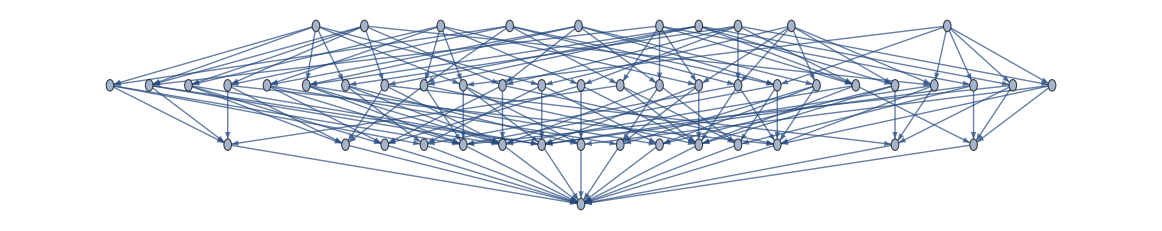

```mathematica
Graph[Map[#[[1]]->#[[2]]&,Select[sss2,Length[ListofVars[#]]==2&]],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
n13x24x5≥n1234x5/.repcolofourrealnullgraph2
```

-Graphics-n13x24x513284≥-Graphics-n1234x557528

```mathematica
Length[%]
```

1895

```mathematica
Length[allGraphs]
```

1895

```mathematica
allGraphs[lambdaKey,"colofour"]
```

v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

## Finding the crossed amigos

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeCount[g]==7 
&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]&& ! MyPlanar[allGraphs,#]
]&]}]
```

{-Graphics-27307,-Graphics-27253,-Graphics-22879,-Graphics-22855,-Graphics-20749}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeCount[g]==6 
&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
]&]}]
```

{-Graphics-27226,-Graphics-22852,-Graphics-20746,-Graphics-20692,-Graphics-20668}

```mathematica
(Table[allGraphs[k,"colofourrealnull"],{k,{27307,27253,20668}}]//Total)*2//Expand
```

52 n12345-14 n1234x5-18 n1235x4-10 n123x45+10 n123x4x5-12 n1245x3+2 n124x3x5-8 n125x34+8 n125x3x4-8 n12x345+6 n12x34x5+2 n12x35x4+6 n12x3x45-6 n12x3x4x5-16 n1345x2-2 n134x25+4 n134x2x5-2 n135x24+6 n135x2x4-4 n13x245+2 n13x24x5+2 n13x25x4+4 n13x2x45-4 n13x2x4x5-6 n145x23+6 n145x2x3-8 n15x234+6 n15x23x4+2 n15x24x3+6 n15x2x34-6 n15x2x3x4-14 n1x2345+8 n1x234x5+4 n1x235x4+6 n1x23x45-6 n1x23x4x5+4 n1x245x3-2 n1x24x3x5+2 n1x25x34-2 n1x25x3x4+8 n1x2x345-6 n1x2x34x5-2 n1x2x35x4-6 n1x2x3x45+6 n1x2x3x4x5

```mathematica
ineqs37=Fold[And,Table[Simplify[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}]
]
```

1
 |  |  |  |

```mathematica
strict =Map[1/6#[[1]]<=#[[2]]≤4/5#[[1]]&, Select[ineqs37,Length[ListofVars[#]]==2&]]
```

n1x2x3x4x5/6≤n12x3x4x5≤(4 n1x2x3x4x5)/5&&n1x2345/6≤n12345≤(4 n1x2345)/5&&n15x234/6≤n12345≤(4 n15x234)/5&&n1x234x5/6≤n1234x5≤(4 n1x234x5)/5&&n14x235/6≤n12345≤(4 n14x235)/5&&n145x23/6≤n12345≤(4 n145x23)/5&&n14x23x5/6≤n1234x5≤(4 n14x23x5)/5&&n1x235x4/6≤n1235x4≤(4 n1x235x4)/5&&n15x23x4/6≤n1235x4≤(4 n15x23x4)/5&&n1x23x4x5/6≤n123x4x5≤(4 n1x23x4x5)/5&&n1x23x45/6≤n123x45≤(4 n1x23x45)/5&&n13x2x4x5/6≤n123x4x5≤(4 n13x2x4x5)/5&&n13x245/6≤n12345≤(4 n13x245)/5&&n135x24/6≤n12345≤(4 n135x24)/5&&n13x24x5/6≤n1234x5≤(4 n13x24x5)/5&&n134x2x5/6≤n1234x5≤(4 n134x2x5)/5&&n134x25/6≤n12345≤(4 n134x25)/5&&n1345x2/6≤n12345≤(4 n1345x2)/5&&n13x25x4/6≤n1235x4≤(4 n13x25x4)/5&&n135x2x4/6≤n1235x4≤(4 n135x2x4)/5&&n13x2x45/6≤n123x45≤(4 n13x2x45)/5&&n1x245x3/6≤n1245x3≤(4 n1x245x3)/5&&n15x24x3/6≤n1245x3≤(4 n15x24x3)/5&&n1x24x3x5/6≤n124x3x5≤(4 n1x24x3x5)/5&&n1x24x35/6≤n124x35≤(4 n1x24x35)/5&&n14x2x3x5/6≤n124x3x5≤(4 n14x2x3x5)/5&&n14x25x3/6≤n1245x3≤(4 n14x25x3)/5&&n145x2x3/6≤n1245x3≤(4 n145x2x3)/5&&n14x2x35/6≤n124x35≤(4 n14x2x35)/5&&n1x25x3x4/6≤n125x3x4≤(4 n1x25x3x4)/5&&n1x25x34/6≤n125x34≤(4 n1x25x34)/5&&n15x2x3x4/6≤n125x3x4≤(4 n15x2x3x4)/5&&n15x2x34/6≤n125x34≤(4 n15x2x34)/5&&n1x2x34x5/6≤n12x34x5≤(4 n1x2x34x5)/5&&n1x2x345/6≤n12x345≤(4 n1x2x345)/5&&n1x2x35x4/6≤n12x35x4≤(4 n1x2x35x4)/5&&n1x2x3x45/6≤n12x3x45≤(4 n1x2x3x45)/5&&n12x3x4x5/6≤n123x4x5≤(4 n12x3x4x5)/5&&n12x345/6≤n12345≤(4 n12x345)/5&&n125x34/6≤n12345≤(4 n125x34)/5&&n12x34x5/6≤n1234x5≤(4 n12x34x5)/5&&n124x3x5/6≤n1234x5≤(4 n124x3x5)/5&&n124x35/6≤n12345≤(4 n124x35)/5&&n1245x3/6≤n12345≤(4 n1245x3)/5&&n12x35x4/6≤n1235x4≤(4 n12x35x4)/5&&n125x3x4/6≤n1235x4≤(4 n125x3x4)/5&&n12x3x45/6≤n123x45≤(4 n12x3x45)/5&&n123x4x5/6≤n1234x5≤(4 n123x4x5)/5&&n123x45/6≤n12345≤(4 n123x45)/5&&n1235x4/6≤n12345≤(4 n1235x4)/5&&n1234x5/6≤n12345≤(4 n1234x5)/5&&n123x4x5/6≤n1235x4≤(4 n123x4x5)/5&&n123x4x5/6≤n123x45≤(4 n123x4x5)/5&&n12x3x4x5/6≤n124x3x5≤(4 n12x3x4x5)/5&&n12x3x45/6≤n1245x3≤(4 n12x3x45)/5&&n125x3x4/6≤n1245x3≤(4 n125x3x4)/5&&n12x35x4/6≤n124x35≤(4 n12x35x4)/5&&n124x3x5/6≤n1245x3≤(4 n124x3x5)/5&&n124x3x5/6≤n124x35≤(4 n124x3x5)/5&&n12x3x4x5/6≤n125x3x4≤(4 n12x3x4x5)/5&&n12x34x5/6≤n125x34≤(4 n12x34x5)/5&&n125x3x4/6≤n125x34≤(4 n125x3x4)/5&&n12x3x4x5/6≤n12x34x5≤(4 n12x3x4x5)/5&&n12x3x45/6≤n12x345≤(4 n12x3x45)/5&&n12x35x4/6≤n12x345≤(4 n12x35x4)/5&&n12x34x5/6≤n12x345≤(4 n12x34x5)/5&&n12x3x4x5/6≤n12x35x4≤(4 n12x3x4x5)/5&&n12x3x4x5/6≤n12x3x45≤(4 n12x3x4x5)/5&&n1x2x3x4x5/6≤n13x2x4x5≤(4 n1x2x3x4x5)/5&&n1x2x345/6≤n1345x2≤(4 n1x2x345)/5&&n15x2x34/6≤n1345x2≤(4 n15x2x34)/5&&n1x25x34/6≤n134x25≤(4 n1x25x34)/5&&n1x2x34x5/6≤n134x2x5≤(4 n1x2x34x5)/5&&n14x2x3x5/6≤n134x2x5≤(4 n14x2x3x5)/5&&n14x2x35/6≤n1345x2≤(4 n14x2x35)/5&&n145x2x3/6≤n1345x2≤(4 n145x2x3)/5&&n14x25x3/6≤n134x25≤(4 n14x25x3)/5&&n1x24x35/6≤n135x24≤(4 n1x24x35)/5&&n1x2x35x4/6≤n135x2x4≤(4 n1x2x35x4)/5&&n15x2x3x4/6≤n135x2x4≤(4 n15x2x3x4)/5&&n15x24x3/6≤n135x24≤(4 n15x24x3)/5&&n1x24x3x5/6≤n13x24x5≤(4 n1x24x3x5)/5&&n1x245x3/6≤n13x245≤(4 n1x245x3)/5&&n1x25x3x4/6≤n13x25x4≤(4 n1x25x3x4)/5&&n1x2x3x45/6≤n13x2x45≤(4 n1x2x3x45)/5&&n13x2x4x5/6≤n134x2x5≤(4 n13x2x4x5)/5&&n13x2x45/6≤n1345x2≤(4 n13x2x45)/5&&n135x2x4/6≤n1345x2≤(4 n135x2x4)/5&&n13x25x4/6≤n134x25≤(4 n13x25x4)/5&&n134x2x5/6≤n1345x2≤(4 n134x2x5)/5&&n134x2x5/6≤n134x25≤(4 n134x2x5)/5&&n13x2x4x5/6≤n135x2x4≤(4 n13x2x4x5)/5&&n13x24x5/6≤n135x24≤(4 n13x24x5)/5&&n135x2x4/6≤n135x24≤(4 n135x2x4)/5&&n13x2x4x5/6≤n13x24x5≤(4 n13x2x4x5)/5&&n13x2x45/6≤n13x245≤(4 n13x2x45)/5&&n13x25x4/6≤n13x245≤(4 n13x25x4)/5&&n13x24x5/6≤n13x245≤(4 n13x24x5)/5&&n13x2x4x5/6≤n13x25x4≤(4 n13x2x4x5)/5&&n13x2x4x5/6≤n13x2x45≤(4 n13x2x4x5)/5&&n1x2x3x4x5/6≤n14x2x3x5≤(4 n1x2x3x4x5)/5&&n1x23x45/6≤n145x23≤(4 n1x23x45)/5&&n1x2x3x45/6≤n145x2x3≤(4 n1x2x3x45)/5&&n15x2x3x4/6≤n145x2x3≤(4 n15x2x3x4)/5&&n15x23x4/6≤n145x23≤(4 n15x23x4)/5&&n1x23x4x5/6≤n14x23x5≤(4 n1x23x4x5)/5&&n1x235x4/6≤n14x235≤(4 n1x235x4)/5&&n1x25x3x4/6≤n14x25x3≤(4 n1x25x3x4)/5&&n1x2x35x4/6≤n14x2x35≤(4 n1x2x35x4)/5&&n14x2x3x5/6≤n145x2x3≤(4 n14x2x3x5)/5&&n14x23x5/6≤n145x23≤(4 n14x23x5)/5&&n145x2x3/6≤n145x23≤(4 n145x2x3)/5&&n14x2x3x5/6≤n14x23x5≤(4 n14x2x3x5)/5&&n14x2x35/6≤n14x235≤(4 n14x2x35)/5&&n14x25x3/6≤n14x235≤(4 n14x25x3)/5&&n14x23x5/6≤n14x235≤(4 n14x23x5)/5&&n14x2x3x5/6≤n14x25x3≤(4 n14x2x3x5)/5&&n14x2x3x5/6≤n14x2x35≤(4 n14x2x3x5)/5&&n1x2x3x4x5/6≤n15x2x3x4≤(4 n1x2x3x4x5)/5&&n1x23x4x5/6≤n15x23x4≤(4 n1x23x4x5)/5&&n1x234x5/6≤n15x234≤(4 n1x234x5)/5&&n1x24x3x5/6≤n15x24x3≤(4 n1x24x3x5)/5&&n1x2x34x5/6≤n15x2x34≤(4 n1x2x34x5)/5&&n15x2x3x4/6≤n15x23x4≤(4 n15x2x3x4)/5&&n15x2x34/6≤n15x234≤(4 n15x2x34)/5&&n15x24x3/6≤n15x234≤(4 n15x24x3)/5&&n15x23x4/6≤n15x234≤(4 n15x23x4)/5&&n15x2x3x4/6≤n15x24x3≤(4 n15x2x3x4)/5&&n15x2x3x4/6≤n15x2x34≤(4 n15x2x3x4)/5&&n1x2x3x4x5/6≤n1x23x4x5≤(4 n1x2x3x4x5)/5&&n1x2x345/6≤n1x2345≤(4 n1x2x345)/5&&n1x25x34/6≤n1x2345≤(4 n1x25x34)/5&&n1x2x34x5/6≤n1x234x5≤(4 n1x2x34x5)/5&&n1x24x3x5/6≤n1x234x5≤(4 n1x24x3x5)/5&&n1x24x35/6≤n1x2345≤(4 n1x24x35)/5&&n1x245x3/6≤n1x2345≤(4 n1x245x3)/5&&n1x2x35x4/6≤n1x235x4≤(4 n1x2x35x4)/5&&n1x25x3x4/6≤n1x235x4≤(4 n1x25x3x4)/5&&n1x2x3x45/6≤n1x23x45≤(4 n1x2x3x45)/5&&n1x23x4x5/6≤n1x234x5≤(4 n1x23x4x5)/5&&n1x23x45/6≤n1x2345≤(4 n1x23x45)/5&&n1x235x4/6≤n1x2345≤(4 n1x235x4)/5&&n1x234x5/6≤n1x2345≤(4 n1x234x5)/5&&n1x23x4x5/6≤n1x235x4≤(4 n1x23x4x5)/5&&n1x23x4x5/6≤n1x23x45≤(4 n1x23x4x5)/5&&n1x2x3x4x5/6≤n1x24x3x5≤(4 n1x2x3x4x5)/5&&n1x2x3x45/6≤n1x245x3≤(4 n1x2x3x45)/5&&n1x25x3x4/6≤n1x245x3≤(4 n1x25x3x4)/5&&n1x2x35x4/6≤n1x24x35≤(4 n1x2x35x4)/5&&n1x24x3x5/6≤n1x245x3≤(4 n1x24x3x5)/5&&n1x24x3x5/6≤n1x24x35≤(4 n1x24x3x5)/5&&n1x2x3x4x5/6≤n1x25x3x4≤(4 n1x2x3x4x5)/5&&n1x2x34x5/6≤n1x25x34≤(4 n1x2x34x5)/5&&n1x25x3x4/6≤n1x25x34≤(4 n1x25x3x4)/5&&n1x2x3x4x5/6≤n1x2x34x5≤(4 n1x2x3x4x5)/5&&n1x2x3x45/6≤n1x2x345≤(4 n1x2x3x45)/5&&n1x2x35x4/6≤n1x2x345≤(4 n1x2x35x4)/5&&n1x2x34x5/6≤n1x2x345≤(4 n1x2x34x5)/5&&n1x2x3x4x5/6≤n1x2x35x4≤(4 n1x2x3x4x5)/5&&n1x2x3x4x5/6≤n1x2x3x45≤(4 n1x2x3x4x5)/5

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
Monitor[Simplify[ineqs37&&strict&&Fold[And,Table[allGraphs[k,"colofourrealnull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]],
Trig->False,ComplexityFunction->MyLeafCount],countDone]
```

1
 |  |  |  |

```mathematica
Monitor[Simplify[ineqs37&&strict&&Fold[And,Table[allGraphs[k,"colofourrealnull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]
&& Fold[And,Table[allGraphs[k,"colofourrealnull"]==0,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]],
Trig->False,ComplexityFunction->MyLeafCount],countDone]
```

1
 |  |  |  |

```mathematica
Table[allGraphs[k,"colofourrealnull"]>0,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]
```

{2 n12345-n1234x5-n135x24-n13x245+n13x24x5>0,2 n12345-n1245x3-n134x25-n14x235+n14x25x3>0,2 n12345-n124x35-n135x24-n1x2345+n1x24x35>0,2 n12345-n124x35-n1345x2-n14x235+n14x2x35>0,2 n12345-n1235x4-n134x25-n13x245+n13x25x4>0}

```mathematica
Simplify[Fold[And,Table[allGraphs[k,"colofourrealnull"]>0,{k,{alfa1Key,beta1Key,gamma1Key,epsilon1Key,delta1Key}}]]&&n13x245==4/5n13x245]
```

2 n12345+n13x24x5>n1234x5+n135x24+n13x245&&2 n12345+n14x25x3>n1245x3+n134x25+n14x235&&2 n12345+n1x24x35>n124x35+n135x24+n1x2345&&2 n12345+n14x2x35>n124x35+n1345x2+n14x235&&2 n12345+n13x25x4>n1235x4+n134x25+n13x245&&n13x245==0

## First with edge deletion

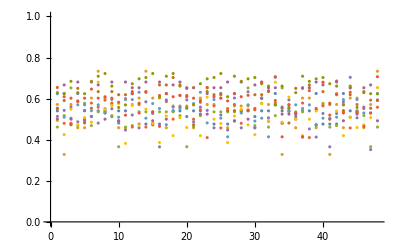

```mathematica
Monitor[
ListPlot[
Table[
Block[{g=Graph[plantri[[k]]],h,base,small},
base=ChromaticPolynomial[g,4];
Table[
h=EdgeDelete[g,e];
small = ChromaticPolynomial[h,4];
base/small
,{e,EdgeList[g]}
]
],
{k,10,20}
],GridLines->{None, {4/5,1/6}},GridLinesStyle->Directive[Red,Thick],PlotRange->{Automatic,{0,1}}],
{k,e}
]
```

## Now with contraction

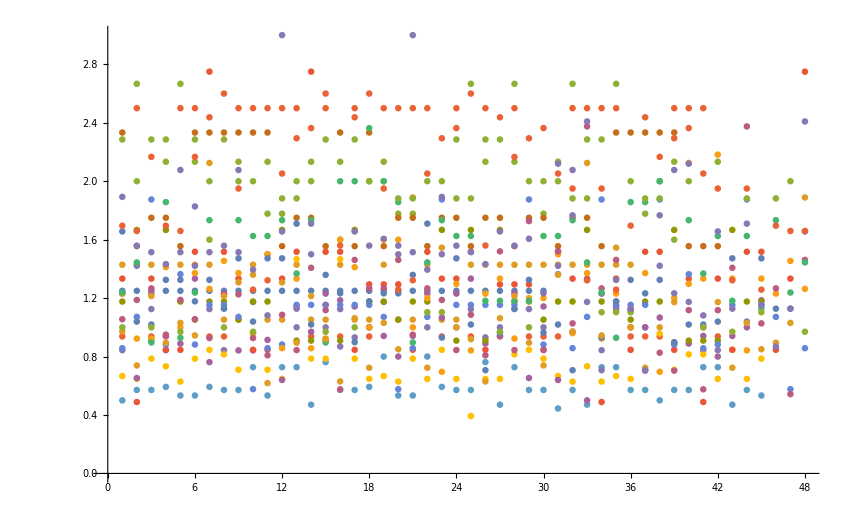

```mathematica
Monitor[
ListPlot[
Table[
Block[{g=Graph[plantri[[k]]],h,base,small},
base=ChromaticPolynomial[g,4];
Table[
h=EdgeContract[g,e];
small = ChromaticPolynomial[h,4];
base/small
,{e,EdgeList[g]}
]
],
{k,1,20}
],GridLines->{None, {5/4,1/6}},GridLinesStyle->Directive[Red,Thick],PlotRange->{Automatic,All}],
{k,e}
]
```

```mathematica
VertexCount[Graph[plantri[[50]]]]
```

20